```mathematica
Clear[P,L,DD,II,EE,nu]
murl = mu -> EE/2/(nu+1);
lamrl = lambda -> EE nu / (1+nu)/(1-2 nu);

sxx=P x y/II;
syy=0;
sxy = P/2/II(DD^2/4-y^2);
u = -P/(2 EE II)(L^2-x^2)y -(P(2+nu))/(6 EE II)y^3 + (P(1+nu)DD^2)/(8 EE II)y//Simplify;
v =(-P L^3)/(6 EE II)(2-3 x/L (1-nu y^2/L^2) + x^3/L^3+3DD^2/4/L^2(1+nu)(1-x/L))//FullSimplify;
(*
u=(-P y)/(6 EE II)((6L-3x)x+(2+nu)(y^2-DD^2/4))
v = -P/(6 EE II)(3 nu y^2(L-x)+(4+5 nu)DD^2 x/4+(3L-x)x^2)*)
```

```mathematica
Integrate[sxy,{y,-DD/2,DD/2}]
```

(DD^3 P)/(12 II)

```mathematica
( (2 mu lambda)/(2 mu + lambda) + mu) Grad[Div[{u,v},{x,y}],{x,y}] + mu  Laplacian[{u,v},{x,y}]/.lamrl/.murl // Simplify
```

{0,0}

```mathematica
(* check *)
Div[{{sxx,sxy},{sxy,syy}},{x,y}]
eps = 1/2(Grad[{u,v},{x,y}] + Transpose@Grad[{u,v},{x,y}]) // Simplify
sigma = (2 mu lambda)/(2 mu + lambda) Tr[eps] IdentityMatrix[2] + 2 mu eps /.murl /.lamrl //FullSimplify
sigma == {{sxx,sxy},{sxy,syy}}//Simplify
```

{0,0}

{{(P x y)/(EE II),((1+nu) P (DD^2-4 y^2))/(8 EE II)},{((1+nu) P (DD^2-4 y^2))/(8 EE II),-(nu P x y)/(EE II)}}

{{(P x y)/II,(P (DD^2-4 y^2))/(8 II)},{(P (DD^2-4 y^2))/(8 II),0}}

True

```mathematica
(* BC *)
u/.{x->L}//Simplify
v/.{x->L}//Simplify
u/.{x->0}//Simplify
v/.{x->0}//Simplify

u/.{y->-DD/2}//Simplify
v/.{y->-DD/2}//Simplify
u/.{y->DD/2}//Simplify
v/.{y->DD/2}//Simplify

sxx/.{x->0};
sxy/.{x->0} // Simplify//FortranForm
```

(P y (3 DD^2 (1+nu)-4 (2+nu) y^2))/(24 EE II)

-(L nu P y^2)/(2 EE II)

(P y (3 DD^2 (1+nu)-4 (3 L^2+(2+nu) y^2)))/(24 EE II)

-((8 L^3+3 DD^2 L (1+nu)) P)/(24 EE II)

-(DD P (DD^2 (1+2 nu)+12 (-L^2+x^2)))/(48 EE II)

-(P (3 DD^2 (L+L nu-x)+4 (L-x)^2 (2 L+x)))/(24 EE II)

(DD P (DD^2 (1+2 nu)+12 (-L^2+x^2)))/(48 EE II)

-(P (3 DD^2 (L+L nu-x)+4 (L-x)^2 (2 L+x)))/(24 EE II)

(P*(DD**2 - 4*y**2))/(8.*II)

```mathematica
uu = {ux[x,y],uy[x,y]};
eps = 1/2(Grad[uu,{x,y}]+Transpose@Grad[uu,{x,y}])
sigma = lambda Tr[eps] IdentityMatrix[2] + 2mu eps // Simplify
sigma.{nx, ny} // Expand //InputForm
```

{{ux^(1,0)[x,y],1/2 (ux^(0,1)[x,y]+uy^(1,0)[x,y])},{1/2 (ux^(0,1)[x,y]+uy^(1,0)[x,y]),uy^(0,1)[x,y]}}

{{lambda uy^(0,1)[x,y]+(lambda+2 mu) ux^(1,0)[x,y],mu (ux^(0,1)[x,y]+uy^(1,0)[x,y])},{mu (ux^(0,1)[x,y]+uy^(1,0)[x,y]),(lambda+2 mu) uy^(0,1)[x,y]+lambda ux^(1,0)[x,y]}}

{mu*ny*Derivative[0, 1][ux][x, y] + lambda*nx*Derivative[0, 1][uy][x, y] + 
  lambda*nx*Derivative[1, 0][ux][x, y] + 2*mu*nx*Derivative[1, 0][ux][x, y] + 
  mu*ny*Derivative[1, 0][uy][x, y], mu*nx*Derivative[0, 1][ux][x, y] + 
  lambda*ny*Derivative[0, 1][uy][x, y] + 2*mu*ny*Derivative[0, 1][uy][x, y] + 
  lambda*ny*Derivative[1, 0][ux][x, y] + mu*nx*Derivative[1, 0][uy][x, y]}

```mathematica
ub = u/.{y->-DD/2}
ut = u/.{y->DD/2}

vb=v/.{y->-DD/2}
vt=v/.{y->DD/2}
```

(DD P (6 L-3 x) x)/(12 EE II)

-(DD P (6 L-3 x) x)/(12 EE II)

-(P (3/4 DD^2 nu (L-x)+1/4 DD^2 (4+5 nu) x+(3 L-x) x^2))/(6 EE II)

-(P (3/4 DD^2 nu (L-x)+1/4 DD^2 (4+5 nu) x+(3 L-x) x^2))/(6 EE II)

```mathematica
Import["~/scripts/math/ToMatlab.m"]
{sxx,syy,sxy,u,v}//ToMatlab
```

ToMatlab::shdw: Symbol ToMatlab appears in multiple contexts {MatlabUtils`ToMatlab`,Global`}; definitions in context MatlabUtils`ToMatlab` may shadow or be shadowed by other definitions.

[II.^(-1).*P.*x.*y,0,(1/2).*II.^(-1).*P.*((1/4).*DD.^2+(-1).*y.^2) ...
  ,(1/24).*EE.^(-1).*II.^(-1).*P.*y.*(3.*DD.^2.*(1+nu)+(-4).*(3.* ...
  L.^2+(-3).*x.^2+(2+nu).*y.^2)),(-1/24).*EE.^(-1).*II.^(-1).*P.*( ...
  3.*DD.^2.*(1+nu).*(L+(-1).*x)+4.*(2.*L.^3+(-3).*L.^2.*x+x.^3+3.* ...
  nu.*x.*y.^2))];

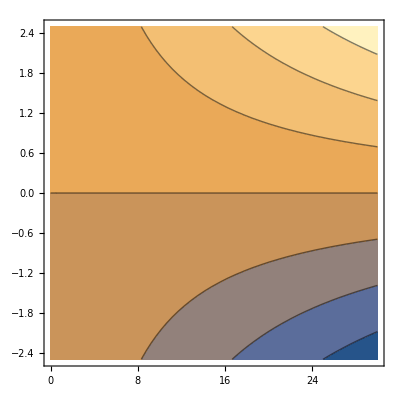
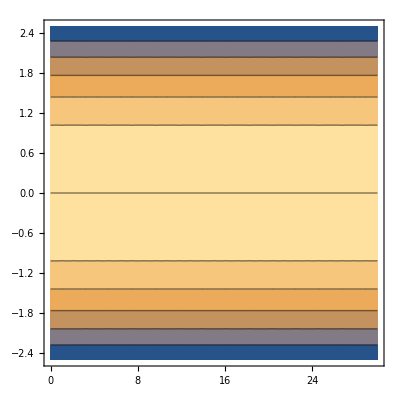
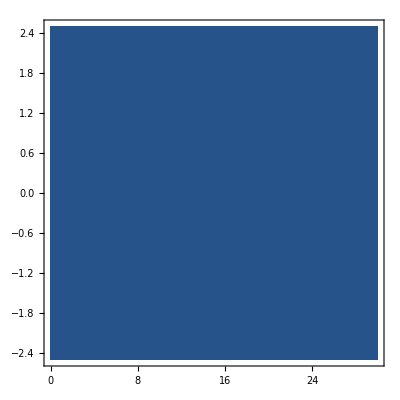

```mathematica
P = 1000;
L = 30;
DD = 5;
II=DD^3/12;
EE=72.1 10^9;
nu = 0.33;
{ContourPlot[sxx,{x,0,L},{y,-DD/2,DD/2}],
ContourPlot[sxy,{x,0,L},{y,-DD/2,DD/2}],
ContourPlot[syy,{x,0,L},{y,-DD/2,DD/2}]}
```

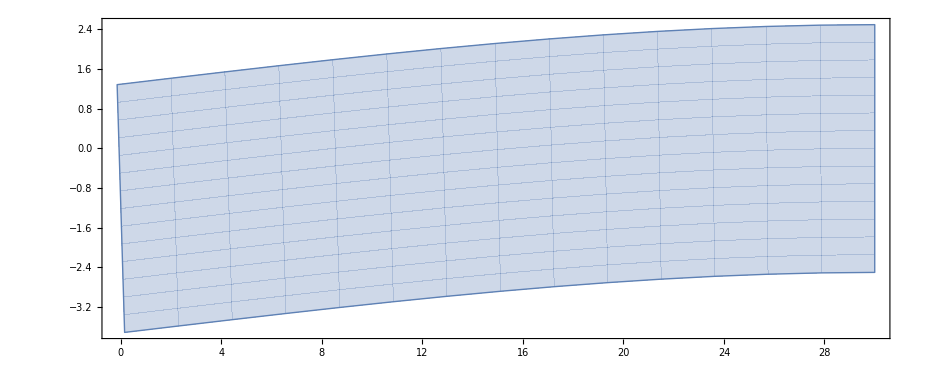

```mathematica
f=10^5;
ParametricPlot[{x+f u,y+f v},{x,0,L},{y,-DD/2,DD/2}]
```

```mathematica
maxu=First@Maximize[{Sqrt[u^2+v^2],0≤x≤ L,-DD/2≤y≤ DD/2},{x,y},Reals]
UnitConvert[Quantity[maxu,"m"],"micrometers"]
```

0.0000122407

12.2407 µm

```mathematica
g = Grad[{u,v},{x,y}];
maxu=First@Maximize[{Norm[g,"Frobenius"],0≤x≤ L,-DD/2≤y≤ DD/2},{x,y},Reals]
```

8.53225×10^-7

```mathematica
a = Log[50];
b=Log[2000];
n = 100;
r = Union@Ceiling@N@Exp[Range[a, b, (b-a)/n]]
```

{50,52,54,56,58,61,63,65,68,70,73,76,78,81,84,87,91,94,98,101,105,109,113,117,122,126,131,136,141,146,152,157,163,169,176,182,189,196,204,211,219,227,236,245,254,263,273,284,294,305,317,329,341,354,367,381,395,410,425,441,458,475,493,511,531,550,571,593,615,638,662,687,712,739,767,796,826,857,889,922,957,993,1030,1069,1109,1151,1194,1239,1285,1333,1384,1435,1489,1545,1603,1664,1726,1791,1858,1928,2000}